```mathematica
Clear["Global`*"]
```

```mathematica
x[t_]=2.9*Cos[3.2*π*t];
y[t_]=Sin[4π*t]+5t;
```

```mathematica
r[t_]={x[t],y[t]};
```

```mathematica
parametricplot=ParametricPlot[r[t],{t,0,1}];
```

When finding the points for the two towns and the pont:

Chateau de Cauchy and Chateau de Laplace:

```mathematica
cauchy = Graphics[{Red, Disk[{x[0],y[0]},0.1]}];
laplace = Graphics[{Blue, Disk[{x[1],y[1]},0.1]}];
```

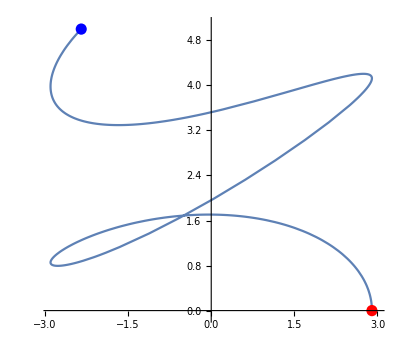

```mathematica
Show[parametricplot,cauchy,laplace,PlotRange->All]
```

```mathematica
guess = Graphics[{Green, Disk[{x[0.4],y[0.4]},0.1]}];
```

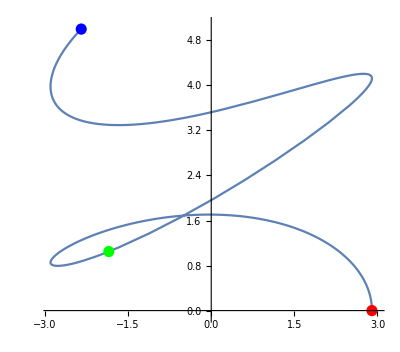

```mathematica
Show[parametricplot,cauchy,laplace,guess,PlotRange->All]
```